```mathematica
ClearAll[]

fact = 178.9818;
time=0.69;
dim=10;

Γ=Import["C:\\Users\\aless\\OneDrive - Università degli Studi di Parma\\Documents\\Lavoro\\QEC_FT\\optimization_codewords\\Gamma_08apr.txt","Table"]*fact;
γ=Array[0,{dim,dim}];
Do[γ[[m,n]]=2*Γ[[m,n]]-Γ[[m,m]]-Γ[[n,n]],{m,dim},{n,dim}];
χ=Exp[γ*time];
{eigs,vecs}=Eigensystem[χ];
(* vecs[[1]]=-vecs[[1]];
vecs[[4]]=-vecs[[4]];*)

Pr=ConstantArray[0,{dim,dim}];
Do[Pr[[k,k]]=1,{k,dim}];

(* Error operators *)
Er =ConstantArray[0,{dim,dim}];
Do[Do[Er[[j,k]]=Er[[j,k]]+Sqrt[eigs[[k]]]*vecs[[k,m]]*Pr[[j,m]],{j,dim},{m,dim}],{k,dim}]
```

```mathematica
(*Er[[All,2]]=-Er[[All,2]];*)
MatrixForm[Er]
```

(-0.643906 | 0.670046 | 0.363526 | 0.0645804 | 0.00927914 | 0.00382407 | 0.000675616 | -0.0000179155 | 3.01086×10^-7 | 0.-3.6478×10^-8 ⅈ
-0.644082 | -0.670137 | 0.36308 | -0.0644165 | 0.00915192 | -0.00383535 | 0.000688936 | 0.0000182288 | 2.81248×10^-7 | 0.+7.86385×10^-9 ⅈ
-0.967979 | 0.153688 | -0.189803 | -0.0573399 | 0.00901923 | 0.00120795 | -0.000911234 | 0.000144912 | 2.44061×10^-6 | 0.-1.80344×10^-6 ⅈ
-0.968089 | -0.152716 | -0.190094 | 0.0570941 | 0.00910107 | -0.00127578 | -0.000917239 | -0.000142539 | 0.0000107261 | 0.+1.20547×10^-6 ⅈ
-0.678128 | 0.660599 | 0.320754 | 0.0276615 | -0.00908658 | -0.00440519 | -0.000839073 | 0.0000237668 | -4.23434×10^-7 | 0.+5.162×10^-8 ⅈ
-0.677857 | -0.660807 | 0.320878 | -0.0279633 | -0.00891745 | 0.00440427 | -0.000853219 | -0.000024097 | -4.06487×10^-7 | 0.-1.13666×10^-8 ⅈ
-0.948949 | 0.262604 | -0.148912 | -0.0913986 | -0.00261019 | 0.000569364 | 0.000359448 | -5.63972×10^-6 | -0.0000187446 | 0.+5.14015×10^-6 ⅈ
-0.948866 | -0.262897 | -0.148823 | 0.0915567 | -0.00263232 | -0.000547379 | 0.000357475 | 7.24187×10^-7 | -0.0000371033 | 0.-2.60224×10^-6 ⅈ
-0.94202 | 0.291193 | -0.134263 | -0.0986668 | -0.0064597 | 0.0000530797 | 0.000720116 | -0.0000840897 | 0.0000153618 | 0.-3.6948×10^-6 ⅈ
-0.941845 | -0.29181 | -0.133989 | 0.098889 | -0.0065235 | 4.92987×10^-6 | 0.000721948 | 0.0000866494 | 0.0000275671 | 0.+1.7432×10^-6 ⅈ)

```mathematica
acc=0;
Do[acc=acc+Er[[k,j]]*Er[[k,j]],{k,dim},{j,dim/2}]
1-acc/dim
```

7.72422×10^-6

```mathematica
b=ConstantArray[0,{dim}];
Do[b[[k]]=1,{k,dim-1,dim}];
B=ConstantArray[0,{dim,dim}];
A=ConstantArray[0,{38,dim}];
z=ConstantArray[0,dim];
zL=ConstantArray[0,{dim}];
oL=ConstantArray[0,{dim}];
ew0=ConstantArray[0,{dim/2,dim}];
ew1=ConstantArray[0,{dim/2,dim}];
inds=Range[8];
```

```mathematica
(* code words*)
x =1;
While[x>1/1000000,
zero=Sort[Join[RandomSample[{1,3,5,7,9},3],RandomSample[{2,4,6,8,10},2]]];
(*zero ={2,4,5,7,9,12};*)
uno=Complement[Range[dim],zero];
cw=Flatten[{zero, uno}];
Do[z[[k]]=1,{k,dim/2+1,dim}];

Do[m=1; Do[Do[A[[m,j]]=Sqrt[eigs[[k]]*eigs[[l]]]*vecs[[l,cw[[j]]]]*vecs[[k,cw[[j]]]]*(-1)^z[[j]];m=m+1,{l,k,dim/2}],{k,1,dim/2}],{j,1,dim}];

Do[B[[j,k]]=A[[inds[[j]],k]],{j,1,dim-2},{k,1,dim}];
Do[B[[dim-1,k]]=z[[k]],{k,1,dim}];
Do[B[[dim,k]]=1-z[[k]],{k,1,dim}];
x=Total[Abs[Im[Sqrt[PseudoInverse[B,Tolerance->10^(-15)].b]]]]]
y=Sqrt[PseudoInverse[B,Tolerance->10^(-15)].b] ;(* we can specify Tolerance --> 0 *)
Det[B]
```

3.37336×10^-20

```mathematica
MatrixForm[y]
```

(0.197082
0.110223
0.222034
0.678311
0.663026
0.198496
0.103428
0.220781
0.686154
0.656011)

```mathematica
Max[Abs[PseudoInverse[B].B-IdentityMatrix[dim]]]
```

7.93079×10^-10

```mathematica
(* determine orthogonal set of error words *)
```

```mathematica
Do[zL[[zero[[k]]]]=Re[y[[k]]],{k,1,dim/2}];
Do[oL[[uno[[k]]]]=Re[y[[k+dim/2]]],{k,1,dim/2}];
Do[ew0[[j,k]]=Er[[k,j]]*zL[[k]],{k,1,dim},{j,1,dim/2}];
Do[ew1[[j,k]]=Er[[k,j]]*oL[[k]],{k,1,dim},{j,1,dim/2}];
Subscript[ψ, 0]=Transpose[Orthogonalize[ew0]]; (* we can specify other method than Gram Schmidt and tolerance *)
Subscript[ψ, 1]=Transpose[Orthogonalize[ew1]];  (* columns are orthogonal error words *)

(* Projectors & Correctors *)
Pp=ConstantArray[0,{dim,dim,dim/2}];
Cr=ConstantArray[0,{dim,dim,dim/2}];
Do[Pp[[j,k,l]]=Subscript[ψ, 0][[j,l]]*Conjugate[Subscript[ψ, 0][[k,l]]]+Subscript[ψ, 1][[j,l]]*Conjugate[Subscript[ψ, 1][[k,l]]],{j,1,dim},{k,1,dim},{l,1,dim/2}];

Do[Subscript[θ, 0]=-ArcCos[Conjugate[zL].Subscript[ψ, 0][[All,k]]]; 
Subscript[θ, 1]=-ArcCos[Conjugate[oL].Subscript[ψ, 1][[All,k]]]; 
Subscript[v, 0]=Normalize[Subscript[ψ, 0][[All,k]]-(Conjugate[zL].Subscript[ψ, 0][[All,k]])*zL];
Subscript[v, 1]=Normalize[Subscript[ψ, 1][[All,k]]-(Conjugate[oL].Subscript[ψ, 1][[All,k]])*oL];
Cr[[All,All,k]]=Cos[Subscript[θ, 0]]*(Outer[Times,zL,Conjugate[zL]]+Outer[Times,Subscript[v, 0],Conjugate[Subscript[v, 0]]])+Sin[Subscript[θ, 0]]*(-Outer[Times,zL,Conjugate[Subscript[v, 0]]]+ Outer[Times,Subscript[v, 0],Conjugate[zL]])+Cos[Subscript[θ, 1]]*(Outer[Times,oL,Conjugate[oL]]+Outer[Times,Subscript[v, 1],Conjugate[Subscript[v, 1]]])+Sin[Subscript[θ, 1]]*(-Outer[Times,oL,Conjugate[Subscript[v, 1]]]+ Outer[Times,Subscript[v, 1],Conjugate[oL]]),{k,1,dim/2}];
```

```mathematica
(* test ideal QEC *)
α=1/Sqrt[2];
β=1/Sqrt[2];
Subscript[ψ, i]=α*zL+β*oL;
ρi=Outer[Times,Subscript[ψ, i],Subscript[ψ, i]];  (* initial state *)
ρ0=ρi;
logspace[a_,b_,n_]:=10^Range[a,b,(b-a)/(n-1)];

times=logspace[-3,0,30];
fid=ConstantArray[0,Length[times]];

Do[Do[ρ0[[j,k]]=Exp[γ[[j,k]]*times[[l]]]*ρi[[j,k]] ,{j,1,dim},{k,1,dim}];
Do[ρ=Cr[[All,All,t]].Pp[[All,All,t]].ρ0.ConjugateTranspose[Pp[[All,All,t]]].ConjugateTranspose[Cr[[All,All,t]]];fid[[l]]=fid[[l]]+Conjugate[Subscript[ψ, i]].ρ.Subscript[ψ, i],{t,1,dim/2}],{l,1,Length[times]}];
```

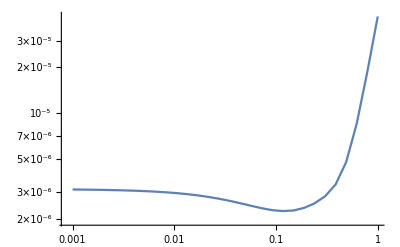

```mathematica
data=Transpose@{times,1-fid};
ListLogLogPlot[data,Joined->True]
```

```mathematica
Re[Log10[1-fid[[1]]]]
```

-5.50469

```mathematica
zero
```

{1,3,6,8,9}